It’s a simple matter to evaluate double integrals in Mathematica, if you know the bounds. It’s not possible to enter a double integral directly: only an iterated integral. As usual, Mathematica will assume you know what you’re doing. It can’t correct errors in the limit functions that appear in the definite integrals. The next few commands draw a polygonal region in the plane. Don’t worry about how they work if you don’t care, I just want you to have a picture to look at. Pictures make everything better. Remember, you need to evaluate each command cell using Shift+Enter (or Enter on the keypad) as you go.

```mathematica
a:={0,0}
b:={1,0}
c:={2,1}
d:={0,1}
```

```mathematica
Vert={a,b,c,d,a}
```

```mathematica
Graphics[Table[Line[{Vert[[k]],Vert[[k+1]]}],{k,1,4}]]
```

The vertices of this 4-gon are (0,0), (1,0), (2,1), and (0,1). It’s a 4-gon conclusion that you should be able to integrate over such a region (simple polygons) in either “order”. To make things very simple we can choose to integrate the constant function 1 over this region. We’ll be finding the volume of the prism whose base is the 4-gon and whose height is 1 (numerically equal to the area of the 4-gon).

Let’s think first about the dx dy order, since this region is horizontally simple. Why is it horizontally simple? Because a point in the 4-gon satisfies some inequalities:

0 ≤ y ≤ 1
0 ≤ x ≤ ?

By inspection or by algebra, we see that an equation of the line containing the slanted side of the 4-gon is y = x - 1. We need the x-bound information to be in terms of y, so we solve this equation for x, obtaining x = y + 1. Our inequalities become.

```mathematica
0≤y≤1
0≤x≤y+1
```

(It is an interesting fact that all polygons are expressible in terms of such linear inequalities; in other words, that a polygon is the same thing as a bounded intersection of finitely many half-planes.) Anyway, this tells us how to integrate over the 4-gon in the dx dy order. To get this iterated integral, I used the Basic Math Assistant palette in the Palettes menu (use the Advanced tab). For integrands involving a plus or minus sign, you should surround them with parentheses. Evaluate the next cell to get the value of the integral:

```mathematica
∫_0^1 ∫_0^(y+1) 1ⅆxⅆy
```

Clearly, this is the area of the 4-gon. In the dy dx order, we have to use two different iterated integrals. This is because there are two different kinds of vertical segment; the region is not vertically simple, but it is the union of two vertically simple regions.

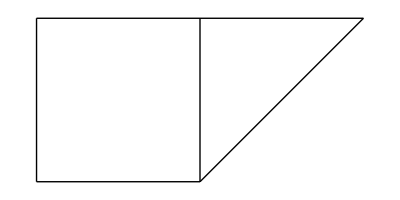

```mathematica
Graphics[{Table[Line[{Vert[[k]],Vert[[k+1]]}],{k,1,4}],Line[{b,{1,1}}]}]
```

In the square, our points satisfy easy inequalities. Both coordinates are sandwiched between 0 and 1. That gives rise to the first iterated integral displayed below. The second one comes from the triangle. The vertical segments that live in the triangle clearly have x between 1 and 2. Fill in the limits by thinking about the inequalities their y-coordinates must satisfy. Remember: your y bounds cannot involve y. Mathematica will nonsensical output if you use the variable of integration in the limits, but it might not complain. It assumes you know what you’re doing. Just click on the boxes where the limits should be to fill them in. Did you get 3/2?

```mathematica
∫_0^1 ∫_0^1 1ⅆyⅆx+∫_0^1 ∫_□^□ 1ⅆyⅆx
```

It’s essential that you draw a picture that is accurate as to how the boundary curves interact with each other. Intersections of the boundary curves are particularly important. If you have the wrong idea of how the region is shaped, it’s easy to get wrong bounds.

The second problem from in class concerned an integral whose bounds were

```mathematica
0≤x≤1
ⅇ^x≤y≤e
```

The region is drawn by the next command.

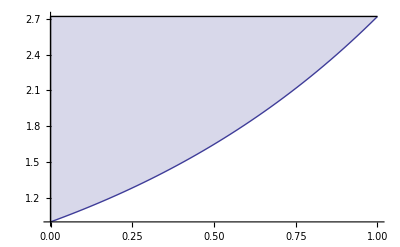

```mathematica
Show[{Plot[Exp[x],{x,0,1},Filling->Top], Graphics[{Line[{{0,1},{0,E}}],Line[{{0,E},{1,E}}]}]}]
```

It’s key to realize that the curved “hypotenuse” of this pseudo-triangle crosses the line x = 1 at the point (1,1). Finding this out is a natural part of drawing the picture. After all, if the “hypotenuse” (the graph of e^x) crosses below this (I use a different function below to achieve this effect), we get a region that is not horizontally simple, something like

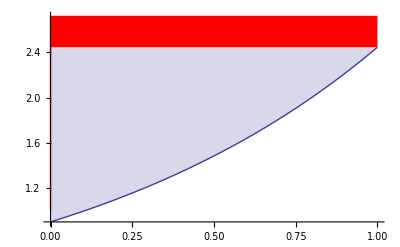

```mathematica
Show[{Plot[0.9Exp[x],{x,0,1},Filling->Top,PlotRange->All], Graphics[{Red,Rectangle[{0,0.9*E},{1,E}],Line[{{0,1},{0,E}}],Line[{{0,E},{1,E}}]}]}]
```

If it crosses above, we still get a simple region, but a different-looking one. Only the stuff below the line y = 1 contributes

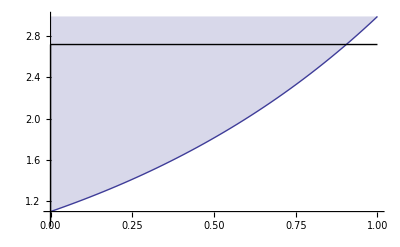

```mathematica
Show[{Plot[1.1Exp[x],{x,0,1},Filling->Top,PlotRange->All], Graphics[{Line[{{0,1},{0,E}}],Line[{{0,E},{1,E}}]}]}]
```

Now that you understand how to use the definite integral button in the Basic Math palette to do double integrals, you should be able to use this worksheet to help you check your WeBWorK and also to practice.